# Dimension

Dimension describes how a region grows when its scale grows. We read it from vertex volumes and ball covers.

The graph distance supplies the scale. The drawing supplies no measurement.

These are readings over finite windows. The lattice scale, the boundary and the shape of the balls can bias them.

## Setup

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

The plane mesh, square tiling and Sierpinski triangle use the large roster size; the Menger carpet uses medium. The reference dimensions of the fractals come from their self-similar pieces and scale factors. The carpet is planar; its reference is not the dimension of the Menger sponge.

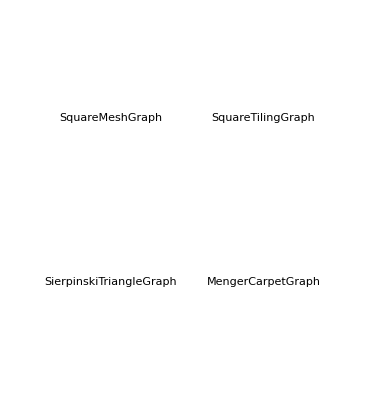

```mathematica
SeedRandom[ 2 ];
dimensionSubstrates = Apply[
  { name, size, reference } |-> With[
    { graph = InfraSubstrate[ name, size, "KeepCoordinates" -> True ] },
    { centre = First @ GraphCenter[ graph ], radius = Floor[ 4 GraphRadius[ graph ] / 5 ] },
    <| "Name" -> name, "Graph" -> graph, "Centre" -> centre, "Radius" -> radius,
      "Reference" -> reference |> ],
  { { "SquareMeshGraph", "Large", 2 }, { "SquareTilingGraph", "Large", 2 },
    { "SierpinskiTriangleGraph", "Large", Log[ 3 ] / Log[ 2 ] },
    { "MengerCarpetGraph", "Medium", Log[ 8 ] / Log[ 3 ] } }, { 1 } ];
GraphicsGrid[ Partition[
  Map[ data |-> Labeled[ data[ "Graph" ], data[ "Name" ] ], dimensionSubstrates ], 2 ] ]
```

## Volume growth

Write V(s)=Abs[B_s(c)] for the number of vertices in the closed ball about a centre.

If V(s) is proportional to s^d, its log-log slope is d.

LogDifferenceQuotientspaclet:WolframInstitute/InfraGeometry/ref/LogDifferenceQuotientsWolframInstitute/InfraGeometry Package Symbol reads successive slopes. DimensionCurvatureFitpaclet:WolframInstitute/InfraGeometry/ref/DimensionCurvatureFitWolframInstitute/InfraGeometry Package Symbol fits their dimension and curvature over a chosen window; VolumeGrowthObservablespaclet:WolframInstitute/InfraGeometry/ref/VolumeGrowthObservablesWolframInstitute/InfraGeometry Package Symbol chooses a window for the Riemannian probes.

The growth dimension once, on the plane mesh: the quotients and the fitted curve. Small radii see individual layers; large radii see the boundary. The fit is a reading over the selected window.

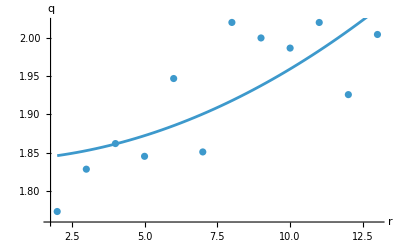
-Graphics-
<|Dimension→1.83984,ScalarCurvature→-0.0125075|>

```mathematica
SeedRandom[ 2 ];
With[
  { graph = dimensionSubstrates[[ 1 ]][ "Graph" ], centre = dimensionSubstrates[[ 1 ]][ "Centre" ] },
  { observables = VolumeGrowthObservables[ graph, centre, "Measure" -> "CountingMeasure" ] },
  { window = observables[ "BallWindow" ], quotients = observables[ "BallLogDifferenceQuotients" ] },
  { points = Table[ { r, quotients[[ r ]] }, { r, window[[ 1 ]], window[[ 2 ]] } ] },
  { fit = DimensionCurvatureFit[ points ] },
  Column[ {
    Show[
      ListPlot[ points, AxesLabel -> { "r", "q" }, PlotRange -> All ],
      Plot[ fit[ "Dimension" ] - fit[ "ScalarCurvature" ] r ( r + 1 ) / ( 3 ( fit[ "Dimension" ] + 2 ) ),
        { r, window[[ 1 ]], window[[ 2 ]] } ] ],
    fit } ] ]
```

## Covering a region

Let N_r(T) be the least number of closed balls of radius r covering the target vertices T. Their centres may be anywhere in the graph.

FindBallCoverpaclet:WolframInstitute/InfraGeometry/ref/FindBallCoverWolframInstitute/InfraGeometry Package Symbol gives the centres. BallCoverNumberpaclet:WolframInstitute/InfraGeometry/ref/BallCoverNumberWolframInstitute/InfraGeometry Package Symbol gives their number. The default method finds a smallest cover; the greedy method gives an upper bound.

We first find an exact cover on a small square tiling. The target is gray and each covering ball has its own colour.

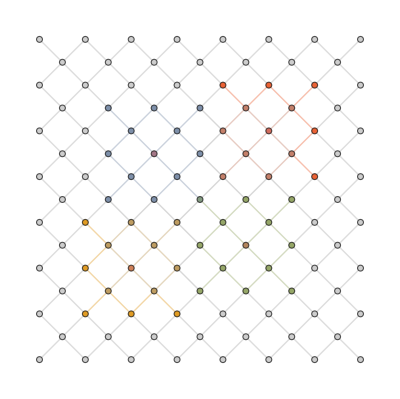
-Graphics-
<|Radius→2,Exact count→4,Covers target→True|>

```mathematica
SeedRandom[ 2 ];
With[
  { graph = InfraSubstrate[ "SquareTilingGraph", "Small", "KeepCoordinates" -> True ] },
  { target = RandomInfraRepresentative[ graph, InfraBall[ First @ GraphCenter[ graph ], 4 ] , "NextVertexFunction" -> Identity ], radius = 2 },
  { centres = FindBallCover[ graph, radius, target ] },
  Column[ {
    InfraSubstrateHighlight[ graph, Join[ { target -> StandardGray },
      MapIndexed[ { centre, index } |-> InfraBall[ centre, radius ] -> ColorData[ 97 ][ First[ index ] ], centres ],
      { centres -> StandardRed } ] ],
    <| "Radius" -> radius, "Exact count" -> BallCoverNumber[ graph, radius, target ],
      "Covers target" -> BallCoverQ[ graph, radius, centres, target ] |> } ] ]
```

The same construction on the larger substrates, now with greedy covers. The target radius is a fixed fraction of the graph radius, and the covering radius a fraction of the target radius.

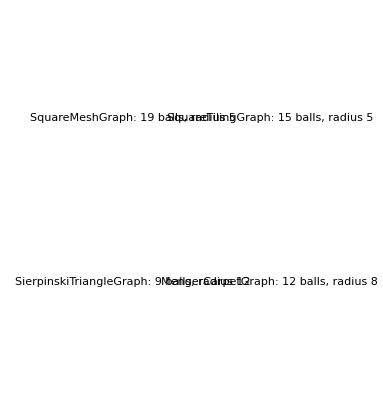

```mathematica
SeedRandom[ 2 ];
GraphicsGrid[ Partition[ Map[
  data |-> With[
    { graph = data[ "Graph" ], centre = data[ "Centre" ], targetRadius = data[ "Radius" ] },
    { radius = Max[ 1, Floor[ targetRadius / 3 ] ], target = RandomInfraRepresentative[ graph, InfraBall[ centre, targetRadius ] , "NextVertexFunction" -> Identity ] },
    { centres = FindBallCover[ graph, radius, target, Method -> "Greedy" ] },
    Labeled[
      InfraSubstrateHighlight[ graph, Join[ { target -> StandardGray },
        MapIndexed[ { point, index } |-> InfraBall[ point, radius ] -> ColorData[ 97 ][ First[ index ] ], centres ],
        { centres -> StandardRed } ] ],
      Row[ { data[ "Name" ], ": ", Length[ centres ], " balls, radius ", radius } ] ] ],
  dimensionSubstrates ], 2 ] ]
```

## Two covering slopes

Box reading. Fix T=B_ρ(c) and vary the covering radius. A d-dimensional region needs approximately r^-d balls.

On a lattice a ball volume is a polynomial in r+1/2. We use this shifted radius for the box slope. Using r at these small radii gives a lower reading.

Growth at a fixed resolution. Fix the covering radius and grow B_s(c). Its covering count is the volume measured in balls of that radius. At radius zero this is exactly the vertex count.

We fit one least-squares slope over each window. Successive quotients of integer covering counts jump and can vanish on plateaux.

The profiles below are computed with greedy covers. The box window ends at half the target radius; the growth window starts beyond the first few layers. The vertex-volume slope uses exactly the growth window.

```mathematica
logSlope[ scales_, counts_ ] :=
  Coefficient[ Fit[ Transpose[ { Log[ N[ scales ] ], Log[ N[ counts ] ] } ], { 1, x }, x ], x ]
```

```mathematica
SeedRandom[ 2 ];
dimensionProfiles = Map[
  data |-> With[
    { graph = data[ "Graph" ], centre = data[ "Centre" ], radius = data[ "Radius" ] },
    { boxRadii = Range[ Floor[ radius / 2 ] ], growthRadii = Range[ 3, radius ],
      target = RandomInfraRepresentative[ graph, InfraBall[ centre, radius ] , "NextVertexFunction" -> Identity ] },
    { boxCounts = Map[ r |-> BallCoverNumber[ graph, r, target, Method -> "Greedy" ], boxRadii ],
      growthCounts = Map[ s |-> BallCoverNumber[ graph, 1,
        RandomInfraRepresentative[ graph, InfraBall[ centre, s ] , "NextVertexFunction" -> Identity ], Method -> "Greedy" ], growthRadii ],
      volumes = Map[ s |-> Length @ RandomInfraRepresentative[ graph, InfraBall[ centre, s ] , "NextVertexFunction" -> Identity ], growthRadii ] },
    Join[ data, <| "BoxRadii" -> boxRadii, "BoxCounts" -> boxCounts,
      "GrowthRadii" -> growthRadii, "GrowthCounts" -> growthCounts, "Volumes" -> volumes,
      "Box" -> -logSlope[ boxRadii + 1/2, boxCounts ], "UnshiftedBox" -> -logSlope[ boxRadii, boxCounts ],
      "Growth" -> logSlope[ growthRadii, growthCounts ], "VertexVolume" -> logSlope[ growthRadii, volumes ] |> ] ],
  dimensionSubstrates ];
GraphicsGrid[ Map[
  data |-> {
    ListLogLogPlot[ Transpose[ { data[ "BoxRadii" ] + 1/2, data[ "BoxCounts" ] } ],
      Joined -> True, AxesLabel -> { "r + 1/2", "cover count" }, PlotLabel -> data[ "Name" ] ],
    ListLogLogPlot[ { Transpose[ { data[ "GrowthRadii" ], data[ "GrowthCounts" ] } ],
      Transpose[ { data[ "GrowthRadii" ], data[ "Volumes" ] } ] }, Joined -> True,
      PlotLegends -> { "radius-one cover", "vertex volume" }, AxesLabel -> { "s", "count" } ] },
  dimensionProfiles ] ]
```

-Graphics-

The normalized profiles against a horizontal target line: the box count multiplied by the shifted radius to the reference dimension, and the growth counts divided by the radius to that dimension. A flat profile supports the reference exponent over that window.

```mathematica
GraphicsGrid[ Map[
  data |-> With[
    { box = data[ "BoxCounts" ] ( data[ "BoxRadii" ] + 1/2 ) ^ data[ "Reference" ],
      growth = data[ "GrowthCounts" ] / data[ "GrowthRadii" ] ^ data[ "Reference" ],
      volume = data[ "Volumes" ] / data[ "GrowthRadii" ] ^ data[ "Reference" ] },
    { Show[
        ListPlot[ Transpose[ { data[ "BoxRadii" ], box / First[ box ] } ], Joined -> True,
          PlotLabel -> data[ "Name" ], AxesLabel -> { "r", "normalized box" }, PlotRange -> All ],
        Plot[ 1, { r, First @ data[ "BoxRadii" ], Last @ data[ "BoxRadii" ] }, PlotStyle -> Dashed ] ],
      Show[
        ListPlot[ { Transpose[ { data[ "GrowthRadii" ], growth / First[ growth ] } ],
          Transpose[ { data[ "GrowthRadii" ], volume / First[ volume ] } ] }, Joined -> True,
          PlotLegends -> { "cover", "vertices" }, AxesLabel -> { "s", "normalized growth" }, PlotRange -> All ],
        Plot[ 1, { s, First @ data[ "GrowthRadii" ], Last @ data[ "GrowthRadii" ] }, PlotStyle -> Dashed ] ] } ],
  dimensionProfiles ] ]
```

-Graphics-

## Readings at this resolution

The table compares the slopes with the reference dimensions. The carpet has a shorter scale window than the other examples. The cover slopes are readings from greedy upper bounds, not certified estimates of the least-cover slopes.

```mathematica
Grid[ Prepend[
  Map[ data |-> Join[ { data[ "Name" ] },
    Map[ value |-> NumberForm[ N[ value ], { 4, 2 } ],
      Lookup[ data, { "Reference", "Box", "UnshiftedBox", "Growth", "VertexVolume" } ] ] ], dimensionProfiles ],
  { "Substrate", "Reference", "Box (shifted)", "Box (unshifted)", "Cover growth", "Vertex growth" } ],
  Frame -> All ]
```

Substrate | Reference | Box (shifted) | Box (unshifted) | Cover growth | Vertex growth
SquareMeshGraph | 2.00 | 1.71 | 1.44 | 1.78 | 1.90
SquareTilingGraph | 2.00 | 1.89 | 1.59 | 1.94 | 1.86
SierpinskiTriangleGraph | 1.58 | 1.47 | 1.31 | 1.47 | 1.46
MengerCarpetGraph | 1.89 | 1.57 | 1.37 | 1.82 | 1.85

## Doubling sees the shape of a ball

A different reading covers B_(2r)(c) by balls of radius r and takes the base-two logarithm of the count.

The square tiling admits a small exact cover. The mesh uses more balls in the greedy cover even though both substrates have planar growth dimension.

A Euclidean disc cannot tile a doubled disc without overlap. Doubling sees this covering overhead as well as the dimension. The greedy mesh count is an upper bound; it does not prove that no smaller cover exists.

The exact square-tiling counts and the greedy mesh counts, computed over interior scales. The pictures show one scale, with each ball in its own colour.

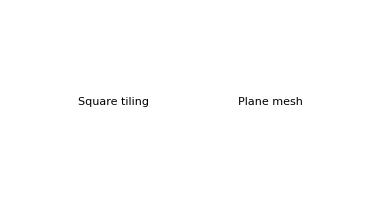
Substrate | Method | r | Cover count | log2 count
Square tiling | Exhaustive | 1 | 4 | 2.00
Square tiling | Exhaustive | 2 | 4 | 2.00
Square tiling | Exhaustive | 3 | 4 | 2.00
Plane mesh | Greedy | 2 | 7 | 2.81
Plane mesh | Greedy | 3 | 7 | 2.81
Plane mesh | Greedy | 4 | 8 | 3.00
Plane mesh | Greedy | 5 | 8 | 3.00
Plane mesh | Greedy | 6 | 8 | 3.00
Plane mesh | Greedy | 7 | 8 | 3.00
Plane mesh | Greedy | 8 | 8 | 3.00
-Graphics-

```mathematica
SeedRandom[ 2 ];
With[
  { square = InfraSubstrate[ "SquareTilingGraph", "Small", "KeepCoordinates" -> True ],
    mesh = dimensionSubstrates[[ 1 ]][ "Graph" ] },
  { cases = { { square, "Square tiling", "Exhaustive", Range[ 1, 3 ] },
      { mesh, "Plane mesh", "Greedy", Range[ 2, 8 ] } } },
  Column[ {
    Grid[ Prepend[ Join @@ Apply[
      { graph, name, method, radii } |-> Map[
        r |-> With[
          { target = RandomInfraRepresentative[ graph, InfraBall[ First @ GraphCenter[ graph ], 2 r ] , "NextVertexFunction" -> Identity ] },
          { count = BallCoverNumber[ graph, r, target, Method -> method ] },
          { name, method, r, count, NumberForm[ N[ Log[ 2, count ] ], { 4, 2 } ] } ], radii ], cases, { 1 } ],
      { "Substrate", "Method", "r", "Cover count", "log2 count" } ], Frame -> All ],
    GraphicsRow[ Apply[
      { graph, name, method, radii } |-> With[
        { r = radii[[ 2 ]], centre = First @ GraphCenter[ graph ] },
        { target = RandomInfraRepresentative[ graph, InfraBall[ centre, 2 r ] , "NextVertexFunction" -> Identity ] },
        { centres = FindBallCover[ graph, r, target, Method -> method ] },
        Labeled[ InfraSubstrateHighlight[ graph, Join[ { target -> StandardGray },
          MapIndexed[ { point, index } |-> InfraBall[ point, r ] -> ColorData[ 97 ][ First[ index ] ], centres ],
          { centres -> StandardRed } ] ], name ] ], cases, { 1 } ] ] } ] ]
```

## The span of points

The ball hull is the intersection of all balls containing the chosen points. InfraBallHullpaclet:WolframInstitute/InfraGeometry/ref/InfraBallHullWolframInstitute/InfraGeometry Package Symbol restricts their radii when a bound is supplied.

In Euclidean space this is the convex hull. For k points in general position its dimension is min (k-1,d).

A pair spans a segment, a triple a triangle. The first full-dimensional hull needs d+1 points.

On a graph we compare the number of hull vertices as the separation L grows. This tests a scaling window, rather than assigning an exact dimension to one finite hull.

On the plane mesh we start at a centre and follow one shortest path for the chosen separation. Each further point is chosen to keep its distances from the earlier points close to that separation. The hulls are blue and their defining points red.

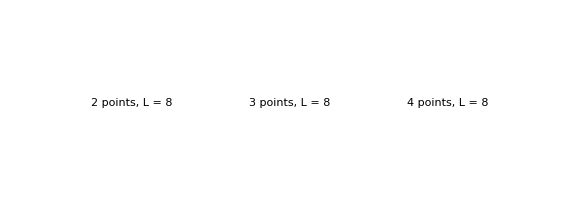

```mathematica
SeedRandom[ 2 ];
planeSpans = With[
  { graph = InfraSubstrate[ "SquareMeshGraph", "Large", "KeepCoordinates" -> True ] },
  { vertices = VertexList[ graph ], distances = GraphDistanceMatrix[ graph ], centre = First @ GraphCenter[ graph ] },
  { endpoint = Last @ MaximalBy[ vertices, v |-> GraphDistance[ graph, centre, v ] ] },
  { path = FindShortestPath[ graph, centre, endpoint ] },
  Map[ spread |-> With[
    { pair = Map[ v |-> VertexIndex[ graph, v ], path[[ { 1, spread + 1 } ]] ] },
    { indices = Nest[ chosen |-> Append[ chosen,
        First @ Ordering[ Total[ Abs[ distances[[ chosen ]] - spread ] ], 1 ] ], pair, 2 ] },
    { seeds = vertices[[ indices ]] },
    <| "Graph" -> graph, "Spread" -> spread, "Seeds" -> seeds,
      "Hulls" -> Table[ RandomInfraRepresentative[ graph, InfraBallHull[ Take[ seeds, k ] ] , "NextVertexFunction" -> Identity ], { k, 2, 4 } ] |> ],
    { 2, 4, 6, 8 } ] ];
GraphicsRow[ Table[ With[
  { data = Last[ planeSpans ] },
  Labeled[ InfraSubstrateHighlight[ data[ "Graph" ],
    { Complement[ data[ "Hulls" ][[ k - 1 ]], Take[ data[ "Seeds" ], k ] ] -> StandardBlue,
      Take[ data[ "Seeds" ], k ] -> { StandardRed, AbsolutePointSize[ 7 ] } } ],
    Row[ { k, " points, L = ", data[ "Spread" ] } ] ] ], { k, 2, 4 } ] ]
```

The table computes the hull volumes and their least-squares log-log slopes. The Euclidean reference exponents are one for the pair and two for both larger sets. The mesh, path direction and short window introduce visible errors; adding a fourth point should not introduce another planar dimension.

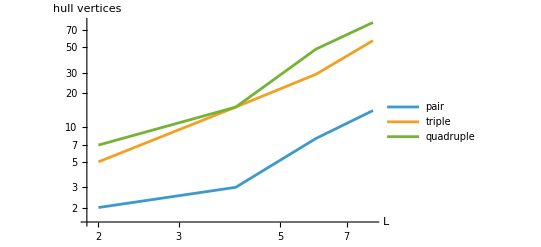
L | Pair | Triple | Quadruple
2 | 2 | 5 | 7
4 | 3 | 15 | 15
6 | 8 | 29 | 48
8 | 14 | 57 | 82
Points | Euclidean exponent | Measured exponent
2 | 1 | 1.41
3 | 2 | 1.72
4 | 2 | 1.81
-Graphics-

```mathematica
With[
  { spreads = Lookup[ planeSpans, "Spread" ], counts = Map[ data |-> Length /@ data[ "Hulls" ], planeSpans ] },
  Column[ {
    Grid[ Prepend[ MapThread[ Prepend, { counts, spreads } ], { "L", "Pair", "Triple", "Quadruple" } ], Frame -> All ],
    Grid[ Prepend[ Table[
      { k, Min[ k - 1, 2 ], NumberForm[ logSlope[ spreads, counts[[ All, k - 1 ]] ], { 4, 2 } ] }, { k, 2, 4 } ],
      { "Points", "Euclidean exponent", "Measured exponent" } ], Frame -> All ],
    ListLogLogPlot[ Map[ volumes |-> Transpose[ { spreads, volumes } ], Transpose[ counts ] ],
      Joined -> True, PlotLegends -> { "pair", "triple", "quadruple" }, AxesLabel -> { "L", "hull vertices" } ] } ] ]
```

The separation stays below half the graph radius. Near the boundary the available ball centres cannot cut away enough vertices, so even the hull of a pair fattens. These finite-window exponents need room around the points.

## A radius bound gives a lens

A bound admits only enclosing balls with radius at most that bound. Increasing it admits more balls, so their intersection shrinks.

Below the least enclosing radius there is no such ball; the empty intersection is the whole graph.

Starting at the least enclosing radius, the lens thins towards the unrestricted ball hull. On a finite mesh the final hull can retain a few vertices across its width.

The same pair is shown under increasing radius bounds, followed by its unrestricted hull. The table also checks that each hull is contained in the preceding one.

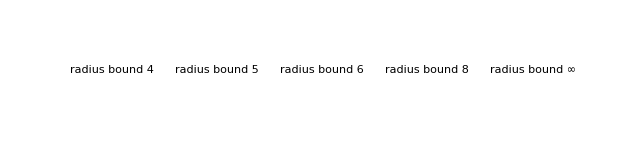
-Graphics-
Radius bound | Hull vertices
4 | 47
5 | 39
6 | 26
8 | 14
∞ | 14
<|Nested→True,Final hull is unrestricted→True|>

```mathematica
SeedRandom[ 2 ];
With[
  { data = Last[ planeSpans ] },
  { graph = data[ "Graph" ], pair = Take[ data[ "Seeds" ], 2 ] },
  { enclosingRadius = Min[ Max /@ Transpose[ GraphDistance[ graph, # ] & /@ pair ] ] },
  { bounds = DeleteDuplicates[ { enclosingRadius, enclosingRadius + 1, enclosingRadius + 2,
      data[ "Spread" ], Infinity } ] },
  { hulls = Map[ bound |-> RandomInfraRepresentative[ graph, InfraBallHull[ pair, bound ] , "NextVertexFunction" -> Identity ], bounds ] },
  Column[ {
    GraphicsRow[ MapThread[ { bound, hull } |-> Labeled[
      InfraSubstrateHighlight[ graph,
        { Complement[ hull, pair ] -> StandardBlue, pair -> { StandardRed, AbsolutePointSize[ 7 ] } } ],
      Row[ { "radius bound ", bound } ] ], { bounds, hulls } ] ],
    Grid[ Prepend[ Transpose[ { bounds, Length /@ hulls } ], { "Radius bound", "Hull vertices" } ], Frame -> All ],
    <| "Nested" -> And @@ MapThread[ SubsetQ, { Most[ hulls ], Rest[ hulls ] } ],
      "Final hull is unrestricted" -> ( Last[ hulls ] === RandomInfraRepresentative[ graph, InfraBallHull[ pair ] , "NextVertexFunction" -> Identity ] ) |> } ] ]
```

## The square-tiling trap

The square tiling has a taxicab metric, whose unit ball is a diamond. The ball hull of two opposite points already fills that diamond. A third point on its side adds nothing. Thus a pair can span an area: the Euclidean span rule depends on the shape of the balls.

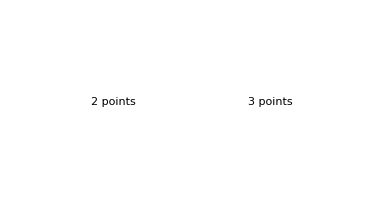
-Graphics-
<|Pair distance→8,Hull volumes→{41,41},Same hull→True|>

```mathematica
SeedRandom[ 2 ];
With[
  { graph = InfraSubstrate[ "SquareTilingGraph", "Large", "KeepCoordinates" -> True ] },
  { centre = First @ GraphCenter[ graph ] },
  { coordinates = GraphEmbedding[ graph ], vertices = VertexList[ graph ] },
  { origin = coordinates[[ VertexIndex[ graph, centre ] ]], neighbours = AdjacencyList[ graph, centre ] },
  { direction = coordinates[[ VertexIndex[ graph, First[ neighbours ] ] ]] - origin },
  { seeds = Map[ offset |-> vertices[[ First @ Ordering[
      Norm /@ ( coordinates - ConstantArray[ origin + offset, Length[ coordinates ] ] ), 1 ] ]],
      { -4 direction, 4 direction, 4 Reverse[ direction ] { -1, 1 } } ] },
  { hulls = Table[ RandomInfraRepresentative[ graph, InfraBallHull[ Take[ seeds, k ] ] , "NextVertexFunction" -> Identity ], { k, 2, 3 } ] },
  Column[ {
    GraphicsRow[ Table[ Labeled[ InfraSubstrateHighlight[ graph,
      { Complement[ hulls[[ k - 1 ]], Take[ seeds, k ] ] -> StandardBlue,
        Take[ seeds, k ] -> { StandardRed, AbsolutePointSize[ 7 ] } } ], Row[ { k, " points" } ] ], { k, 2, 3 } ] ],
    <| "Pair distance" -> GraphDistance[ graph, Sequence @@ Take[ seeds, 2 ] ],
      "Hull volumes" -> ( Length /@ hulls ), "Same hull" -> ( First[ hulls ] === Last[ hulls ] ) |> } ] ]
```

## The span in a cube mesh

The four pictures show nested hulls of two through five points at separation four. The third direction can open when a fourth point is added. The large roster mesh is too coarse for a useful three-dimensional exponent window, so these are pictures of spans rather than a dimension fit.

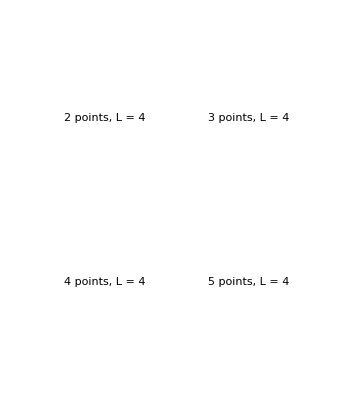
-Graphics-
Points | Hull vertices
2 | 8
3 | 22
4 | 44
5 | 62

```mathematica
SeedRandom[ 2 ];
With[
  { graph = InfraSubstrate[ "CubeMeshGraph", "Large", "KeepCoordinates" -> True,
      EdgeStyle -> Directive[ StandardGray, Opacity[ 0.08 ] ], VertexStyle -> Directive[ StandardGray, Opacity[ 0.08 ] ] ], spread = 4 },
  { vertices = VertexList[ graph ], distances = GraphDistanceMatrix[ graph ], centre = First @ GraphCenter[ graph ] },
  { endpoint = Last @ MaximalBy[ vertices, v |-> GraphDistance[ graph, centre, v ] ] },
  { path = FindShortestPath[ graph, centre, endpoint ] },
  { pair = Map[ v |-> VertexIndex[ graph, v ], path[[ { 1, spread + 1 } ]] ] },
  { indices = Nest[ chosen |-> Append[ chosen,
      First @ Ordering[ Total[ Abs[ distances[[ chosen ]] - spread ] ], 1 ] ], pair, 3 ] },
  { seeds = vertices[[ indices ]] },
  { hulls = Table[ RandomInfraRepresentative[ graph, InfraBallHull[ Take[ seeds, k ] ] , "NextVertexFunction" -> Identity ], { k, 2, 5 } ] },
  Column[ {
    GraphicsGrid[ Partition[ Table[ Labeled[ InfraSubstrateHighlight[ graph,
      { Complement[ hulls[[ k - 1 ]], Take[ seeds, k ] ] -> StandardBlue,
        Take[ seeds, k ] -> { StandardRed, AbsolutePointSize[ 7 ] } },
      "PointSizeRange" -> 4 ],
      Row[ { k, " points, L = ", spread } ] ], { k, 2, 5 } ], 2 ] ],
    Grid[ Prepend[ Transpose[ { Range[ 2, 5 ], Length /@ hulls } ], { "Points", "Hull vertices" } ], Frame -> All ] } ] ]
```

## Related readings

Volume Measurementpaclet:WolframInstitute/InfraGeometry/tutorial/VolumeMeasurementTutorial compares counting and Riemannian measures of balls, shells and tubes.

MetricDimensionpaclet:WolframInstitute/InfraGeometry/ref/MetricDimensionWolframInstitute/InfraGeometry Package Symbol is a different graph invariant: the size of a resolving set, whose distance coordinates distinguish the vertices.

Related Guides

InfraTopologypaclet:WolframInstitute/InfraGeometry/guide/InfraTopology ▪ RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry

Related Tech Notes

VolumeMeasurementTutorialpaclet:WolframInstitute/InfraGeometry/tutorial/VolumeMeasurementTutorial

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/DimensionTutorial

### Keywords

dimension

volume growth

ball cover

box dimension

doubling

Sierpinski triangle

Menger carpet